# LFHQCD: GPD

## Initialize

```mathematica
Clear["Global`*"];
```

```mathematica
Format[x,TraditionalForm]:=Style["x",FontColor->Blue];
Format[at,TraditionalForm]:=Style["a_⊥",FontColor->Blue];
Format[bt,TraditionalForm]:=Style["b_⊥",FontColor->Blue];
Format[kt,TraditionalForm]:=Style["k_⊥",FontColor->Blue];
Format[tau,TraditionalForm]:=Style["τ",FontColor->Red];Format[Q,TraditionalForm]:=Style["Q",FontColor->Blue];Format[qt,TraditionalForm]:=Style["q_⊥",FontColor->Blue];
Format[t,TraditionalForm]:=Style["t",FontColor->Blue];
```

## Form Factor

```mathematica
FF[var_,par_]:=Module[{Q2=var[[1]],τ=var[[2]],λ=par[[1]],Ntau},Ntau=√π Gamma[τ-1]/Gamma[τ-1/2];Beta[τ-1,1/2+Q2/(4 λ)]/Ntau];
```

```mathematica
F1pion[var_,par_]:=Module[{Q2=var[[1]],λ=par[[1]],C4=par[[2]],tw2,tw4},tw2=FF[{Q2,2},{λ}];tw4=FF[{Q2,4},{λ}];(1-C4) tw2+C4 tw4];
```

```mathematica
F1proton[var_,par_]:=Module[{Q2=var[[1]],λ=par[[1]],r=par[[2]],tw3,tw4},tw3=FF[{Q2,3},{λ}];tw4=FF[{Q2,4},{λ}];tw3];
F1neutron[var_,par_]:=Module[{Q2=var[[1]],λ=par[[1]],r=par[[2]],tw3,tw4},tw3=FF[{Q2,3},{λ}];tw4=FF[{Q2,4},{λ}];-r/3 (tw3-tw4)];
```

```mathematica
F2proton[var_,par_]:=Module[{Q2=var[[1]],λ=par[[1]],C6=par[[2]],χp=1.793,tw4,tw6},tw4=FF[{Q2,4},{λ}];tw6=FF[{Q2,6},{λ}];χp ((1-C6) tw4+C6 tw6)];
F2neutron[var_,par_]:=Module[{Q2=var[[1]],λ=par[[1]],C6=par[[2]],χn=-1.913,tw4,tw6},tw4=FF[{Q2,4},{λ}];tw6=FF[{Q2,6},{λ}];χn ((1-C6) tw4+C6 tw6)];
```

## GPD

```mathematica
w[var_,par_]:=Module[{x=var[[1]],λ=par[[1]],a=par[[2]]},x^(1-x) Exp[-a (1-x)^2]];
dw[var_,par_]:=Module[{x=var[[1]],λ=par[[1]],a=par[[2]],x0,λ0,a0},(D[w[{x0},{λ0,a0}],x0])/.{x0->x,λ0->λ,a0->a}];
f[var_,par_]:=Module[{x=var[[1]],λ=par[[1]],a=par[[2]],Wx},Wx=w[{x},{λ,a}];1/(4 λ) Log[1/Wx]];
```

```mathematica
qtau[var_,par_]:=Module[{x=var[[1]],τ=var[[2]],λ=par[[1]],a=par[[2]],Ntau,wx,dwx},Ntau=√π Gamma[τ-1]/Gamma[τ-1/2];wx=w[{x},{λ,a}];dwx=dw[{x},{λ,a}];1/Ntau (1-wx)^(τ-2) wx^(-1/2) dwx];
GPDtau[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],τ=var[[3]],λ=par[[1]],a=par[[2]],qx,fx},qx=qtau[{x,τ},{λ,a}];fx=f[{x,τ},{λ,a}];qx Exp[-Q2 fx]];
```

```mathematica
IPDtau[var_,par_]:=Module[{x=var[[1]],a2=var[[2]],τ=var[[3]],λ=par[[1]],a=par[[2]],qx,fx},qx=qtau[{x,τ},{λ,a}];fx=f[{x,τ},{λ,a}];qx 1/(4 π fx) Exp[-a2/(4 fx)]];
a2mean[var_,par_]:=Module[{},4 f[var,par]];
```

```mathematica
GPDpionHuv[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],λ=par[[1]],a=par[[2]],C4=par[[3]],H2,H4},H2=GPDtau[{x,Q2,2},{λ,a}];H4=GPDtau[{x,Q2,4},{λ,a}];(1-C4) H2+C4 H4];
IPDpionHuv[var_,par_]:=Module[{x=var[[1]],a2=var[[2]],λ=par[[1]],a=par[[2]],C4=par[[3]],H2,H4},H2=IPDtau[{x,a2,2},{λ,a}];H4=IPDtau[{x,a2,4},{λ,a}];(1-C4) H2+C4 H4];
```

```mathematica
GPDprotonHuv[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],λ=par[[1]],a=par[[2]],r=par[[3]],H3,H4},H3=GPDtau[{x,Q2,3},{λ,a}];H4=GPDtau[{x,Q2,4},{λ,a}];(2-r/3) H3+r/3 H4];
GPDprotonHdv[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],λ=par[[1]],a=par[[2]],r=par[[3]],H3,H4},H3=GPDtau[{x,Q2,3},{λ,a}];H4=GPDtau[{x,Q2,4},{λ,a}];(1-(2 r)/3) H3+(2 r)/3 H4];
IPDprotonHuv[var_,par_]:=Module[{x=var[[1]],a2=var[[2]],λ=par[[1]],a=par[[2]],r=par[[3]],H3,H4},H3=IPDtau[{x,a2,3},{λ,a}];H4=IPDtau[{x,a2,4},{λ,a}];(2-r/3) H3+r/3 H4];
IPDprotonHdv[var_,par_]:=Module[{x=var[[1]],a2=var[[2]],λ=par[[1]],a=par[[2]],r=par[[3]],H3,H4},H3=IPDtau[{x,a2,3},{λ,a}];H4=IPDtau[{x,a2,4},{λ,a}];(1-(2 r)/3) H3+(2 r)/3 H4];
```

```mathematica
GPDprotonEuv[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],λ=par[[1]],a=par[[2]],gp=par[[3]],gn=par[[4]],χp=1.793,χn=-1.913,C6,H4,H6},C6=(2 gp χp+gn χn)/(2 χp+χn);H4=GPDtau[{x,Q2,4},{λ,a}];H6=GPDtau[{x,Q2,6},{λ,a}];(1-C6) H4+C6 H6];
GPDprotonEdv[var_,par_]:=Module[{x=var[[1]],Q2=var[[2]],λ=par[[1]],a=par[[2]],gp=par[[3]],gn=par[[4]],χp=1.793,χn=-1.913,C6,H4,H6},C6=(2 gn χn+gp χp)/(2 χn+χp);H4=GPDtau[{x,Q2,4},{λ,a}];H6=GPDtau[{x,Q2,6},{λ,a}];(1-C6) H4+C6 H6];
```

```mathematica
rhoproton[var_,par_]:=Module[{a2=var[[1]],λ=par[[1]],a=par[[2]],r=par[[3]],ru,rd},ru=NIntegrate[IPDprotonHuv[{x,a2},{λ,a,r}],{x,0.0001,0.9999}];rd=NIntegrate[IPDprotonHdv[{x,a2},{λ,a,r}],{x,0.0001,0.9999}];2/3 ru-1/3 rd];
rhoneutron[var_,par_]:=Module[{a2=var[[1]],λ=par[[1]],a=par[[2]],r=par[[3]],ru,rd},ru=NIntegrate[IPDprotonHdv[{x,a2},{λ,a,r}],{x,0.0001,0.9999}];rd=NIntegrate[IPDprotonHuv[{x,a2},{λ,a,r}],{x,0.0001,0.9999}];2/3 ru-1/3 rd];
```

## Plots

### Form factors

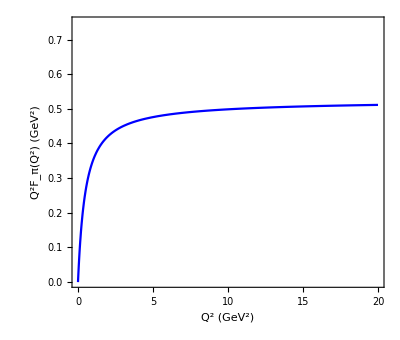

```mathematica
figF1pion=Plot[Q2 F1pion[{Q2},{0.5482^2,0.125}],{Q2,0,20},PlotRange->{{0,20},{0,0.75}},PlotStyle->{Blue,Thickness[0.004]},Frame->True,AspectRatio->0.85,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->18,FrameLabel->{Style["Q^2 (GeV^2)",20,FontFamily->"Times"],Style["Q^2F_π(Q^2) (GeV^2)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1pion.pdf",figF1pion,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1pion.pdf

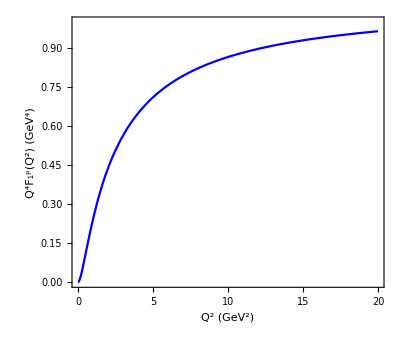

```mathematica
figF1proton=Plot[{Q2^2 F1proton[{Q2},{0.5482^2,1.5}]},{Q2,0,20},PlotRange->{{0,20},{0,1}},PlotStyle->{{Blue,Thickness[0.004]}},Frame->True,AspectRatio->0.85,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->18,FrameLabel->{Style["Q^2 (GeV^2)",20,FontFamily->"Times"],Style["Q^4F_1^p(Q^2) (GeV^4)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1proton.pdf",figF1proton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1proton.pdf

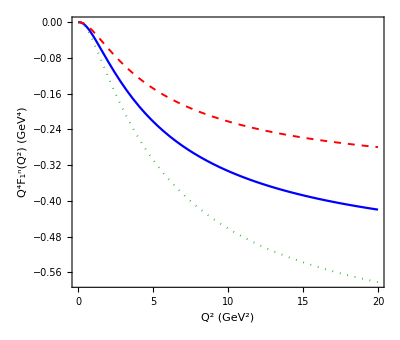

```mathematica
figF1neutron=Plot[{Q2^2 F1neutron[{Q2},{0.5482^2,1.5}],Q2^2 F1neutron[{Q2},{0.5482^2,1.0}],Q2^2 F1neutron[{Q2},{0.5482^2,2.08}]},{Q2,0,20},PlotRange->{{0,20},Full},PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.0035]},{Darker[Green],Dotted,Thickness[0.0035]}},Frame->True,AspectRatio->0.85,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->18,FrameLabel->{Style["Q^2 (GeV^2)",20,FontFamily->"Times"],Style["Q^4F_1^n(Q^2) (GeV^4)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1neutron.pdf",figF1neutron,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f1neutron.pdf

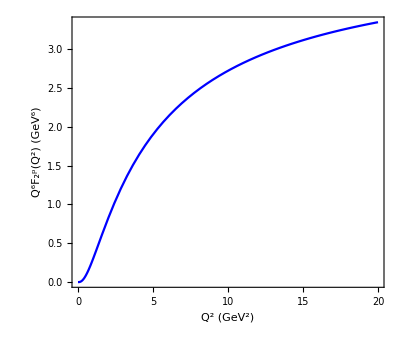

```mathematica
figF2proton=Plot[{Q2^3 F2proton[{Q2},{0.5482^2,0.27}]},{Q2,0,20},PlotRange->{{0,20},Full},PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.0035]},{Darker[Green],Dotted,Thickness[0.0035]}},Frame->True,AspectRatio->0.85,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->18,FrameLabel->{Style["Q^2 (GeV^2)",20,FontFamily->"Times"],Style["Q^6F_2^p(Q^2) (GeV^6)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f2proton.pdf",figF2proton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f2proton.pdf

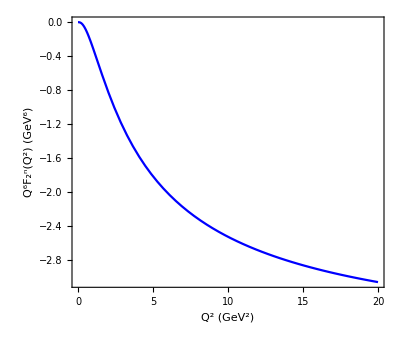

```mathematica
figF2neutron=Plot[{Q2^3 F2neutron[{Q2},{0.5482^2,0.38}]},{Q2,0,20},PlotRange->{{0,20},Full},PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.0035]},{Darker[Green],Dotted,Thickness[0.0035]}},Frame->True,AspectRatio->0.85,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->18,FrameLabel->{Style["Q^2 (GeV^2)",20,FontFamily->"Times"],Style["Q^6F_2^n(Q^2) (GeV^6)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f2neutron.pdf",figF2neutron,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/f2neutron.pdf

### GPDs

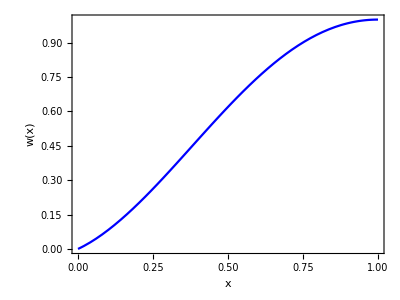

```mathematica
figwx=Plot[{w[{x},{0.5482^2,0.494}],w[{x},{0.5482^2,0.568}],w[{x},{0.5482^2,0.531}]},{x,0,1},PlotRange->{{0,1},{0,1}},Filling->{1->{2}},FillingStyle->{Opacity[0,Red]},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Opacity[0,Blue],Thickness[0]},{Opacity[0,Blue],Thickness[0]},{Blue,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["w(x)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/wx.pdf",figwx,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/wx.pdf

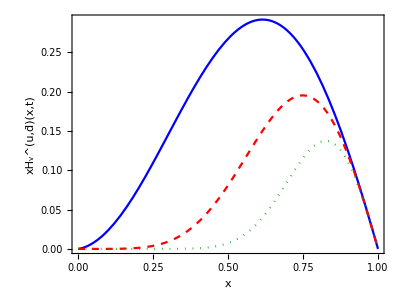

```mathematica
figHqvpion=Plot[{x GPDpionHuv[{x,1},{0.5482^2,0.531,0.125}],x GPDpionHuv[{x,4},{0.5482^2,0.531,0.125}],x GPDpionHuv[{x,10},{0.5482^2,0.531,0.125}]},{x,0,1},PlotRange->{{0,1},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["xH_v^(u,d̄)(x,t)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hvpion.pdf",figHqvpion,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hvpion.pdf

```mathematica
figHqvpion3D=Plot3D[{x GPDpionHuv[{x,t},{0.5482^2,0.531,0.125}]},{x,0,1},{t,10,0},PlotRange->{{0,1},{10,0},Full},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["-t (GeV^2)",20,FontFamily->"Times",Black],Style["xH_v^(u,d̄)",20,FontFamily->"Times",Black]},ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hvpion3d.pdf",figHqvpion3D,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hvpion3d.pdf

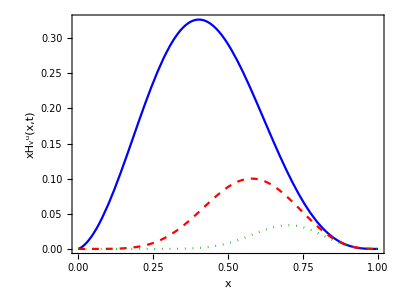

```mathematica
figHuvproton=Plot[{x GPDprotonHuv[{x,1},{0.5482^2,0.531,1.5}],x GPDprotonHuv[{x,4},{0.5482^2,0.531,1.5}],x GPDprotonHuv[{x,10},{0.5482^2,0.531,1.5}]},{x,0,1},PlotRange->{{0,1},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["xH_v^u(x,t)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/huvproton.pdf",figHuvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/huvproton.pdf

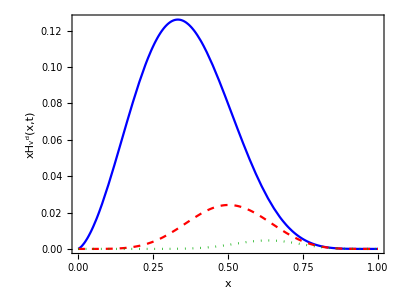

```mathematica
figHdvproton=Plot[{x GPDprotonHdv[{x,1},{0.5482^2,0.531,1.5}],x GPDprotonHdv[{x,4},{0.5482^2,0.531,1.5}],x GPDprotonHdv[{x,10},{0.5482^2,0.531,1.5}]},{x,0,1},PlotRange->{{0,1},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["xH_v^d(x,t)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hdvproton.pdf",figHdvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hdvproton.pdf

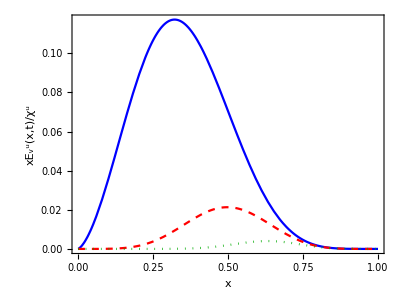

```mathematica
figEuvproton=Plot[{x GPDprotonEuv[{x,1},{0.5482^2,0.531,0.27,0.38}],x GPDprotonEuv[{x,4},{0.5482^2,0.531,0.27,0.38}],x GPDprotonEuv[{x,10},{0.5482^2,0.531,0.27,0.38}]},{x,0,1},PlotRange->{{0,1},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["xE_v^u(x,t)/χ^u",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/euproton.pdf",figEuvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/euproton.pdf

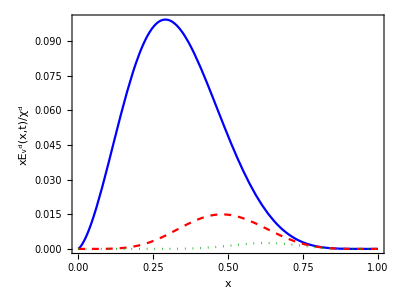

```mathematica
figEdvproton=Plot[{x GPDprotonEdv[{x,1},{0.5482^2,0.531,0.27,0.38}],x GPDprotonEdv[{x,4},{0.5482^2,0.531,0.27,0.38}],x GPDprotonEdv[{x,10},{0.5482^2,0.531,0.27,0.38}]},{x,0,1},PlotRange->{{0,1},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["x",20,FontFamily->"Times"],Style["xE_v^d(x,t)/χ^d",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/edproton.pdf",figEdvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/edproton.pdf

```mathematica
figHuvproton3D=Plot3D[{x GPDprotonHuv[{x,t},{0.5482^2,0.531,1.5}]},{x,0,1},{t,10,0},PlotRange->{{0,1},{0,10},Full},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["-t (GeV^2)",20,FontFamily->"Times",Black],Style["xH_v^u",20,FontFamily->"Times",Black]},ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/huvproton3d.pdf",figHuvproton3D,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/huvproton3d.pdf

```mathematica
figHdvproton3D=Plot3D[{x GPDprotonHdv[{x,t},{0.5482^2,0.531,1.5}]},{x,0,1},{t,0,10},PlotRange->{{0,1},{0,10},Full},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["-t (GeV^2)",20,FontFamily->"Times",Black],Style["xH_v^d",20,FontFamily->"Times",Black]},ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hdvproton3d.pdf",figHdvproton3D,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/hdvproton3d.pdf

```mathematica
figEuvproton3D=Plot3D[{x GPDprotonEuv[{x,t},{0.5482^2,0.531,0.27,0.38}]},{x,0,1},{t,10,0},PlotRange->{{0,1},{10,0},Full},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["-t (GeV^2)",20,FontFamily->"Times",Black],Style["xE_v^u/χ^u",20,FontFamily->"Times",Black]},ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/euproton3d.pdf",figEuvproton3D,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/euproton3d.pdf

```mathematica
figEdvproton3D=Plot3D[{x GPDprotonEdv[{x,t},{0.5482^2,0.531,0.27,0.38}]},{x,0,1},{t,10,0},PlotRange->{{0,1},{10,0},Full},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["-t (GeV^2)",20,FontFamily->"Times",Black],Style["xE_v^d/χ^d",20,FontFamily->"Times",Black]},ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/edproton3d.pdf",figEdvproton3D,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/edproton3d.pdf

### IPDs

```mathematica
figHtildevpion=Plot3D[{IPDpionHuv[{x,b^2/0.197^2},{0.5482^2,0.531,0.125}]},{x,0.0005,1},{b,-1,1},PlotRange->{{0,1},{-1,1},{0,0.3}},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["a_⊥ (fm)",20,FontFamily->"Times",Black],Rotate[Style["q_v(x,a_⊥) (GeV^2)",20,FontFamily->"Times",Black],π/2]},ColorFunction->Function[x,ColorData["Rainbow"][1-x]],ColorFunctionScaling->True,PlotPoints->120,ViewPoint->{1.5 Pi,-0.7 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildevpion3d.pdf",figHtildevpion,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildevpion3d.pdf

```mathematica
figHtildeuvproton=Plot3D[{IPDprotonHuv[{x,b^2/0.197^2},{0.5482^2,0.531,1.5}]},{x,0.001,1},{b,-1,1},PlotRange->{{0,1},{-1,1},{0,0.5}},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["a_⊥ (fm)",20,FontFamily->"Times",Black],Rotate[Style["u_v(x,a_⊥) (GeV^2)",20,FontFamily->"Times",Black],π/2]},ColorFunction->Function[x,ColorData["Rainbow"][1-x]],ColorFunctionScaling->True,PlotPoints->120,ViewPoint->{1.5 Pi,-0.7 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildeuvproton3d.pdf",figHtildeuvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildeuvproton3d.pdf

```mathematica
figHtildedvproton=Plot3D[{IPDprotonHdv[{x,b^2/0.197^2},{0.5482^2,0.531,1.5}]},{x,0.001,1},{b,-1,1},PlotRange->{{0,1},{-1,1},{0,0.3}},BoxRatios->{1,1,0.618},TicksStyle->Directive[Black,18],AxesLabel->{Style["x",20,FontFamily->"Times",Black],Style["a_⊥ (fm)",20,FontFamily->"Times",Black],Rotate[Style["d_v(x,a_⊥) (GeV^2)",20,FontFamily->"Times",Black],π/2]},ColorFunction->Function[x,ColorData["Rainbow"][1-x]],ColorFunctionScaling->True,PlotPoints->120,ViewPoint->{1.5 Pi,-0.7 Pi,2.0}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildedvproton3d.pdf",figHtildedvproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/htildedvproton3d.pdf

```mathematica
figsize3d=ParametricPlot3D[{{x,y,Sqrt[0.197^2 a2mean[{x},{0.5482^2,0.531}]-y^2]},{x,y,-Sqrt[0.197^2 a2mean[{x},{0.5482^2,0.531}]-y^2]}},{x,0.01,1},{y,-1,1},PlotRange->{{0,1},{-0.99,0.99},{-0.99,0.99}},BoxRatios->{1, 1, 1},TicksStyle->Directive[Black, Thickness[0.003],18],AxesLabel->{Style["x",20,Black,FontFamily->"Times"],Rotate[Style["a_y (fm)",20,Black,FontFamily->"Times"],0],Rotate[Style["a_x (fm)",20,Black,FontFamily->"Times"],0]},TicksStyle->Directive[Black, 18],ColorFunction->Function[x,ColorData["Rainbow"][1-x]],ColorFunctionScaling->True,MeshStyle->{{Gray, Thickness[0.002]},{Gray, Thickness[0.002]}},Mesh->{9,11},PlotPoints->100,ViewPoint->{0.7 Pi,-1.5 Pi,2.0},BoundaryStyle->{Thickness[0.002], Darker[Gray]}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/transversesize.pdf",figsize3d,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/transversesize.pdf

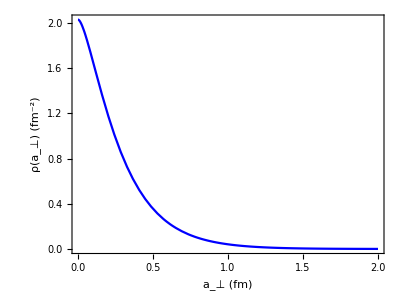

```mathematica
figrhoproton=Plot[{1/0.197^2 rhoproton[{a^2/0.197^2},{0.5482^2,0.531,1.5}]},{a,0,2},PlotRange->{{0,2},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Blue,Thickness[0.004]},FrameTicksStyle->18,FrameLabel->{Style["a_⊥ (fm)",20,FontFamily->"Times"],Style["ρ(a_⊥) (fm^-2)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/rhoproton.pdf",figrhoproton,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/rhoproton.pdf

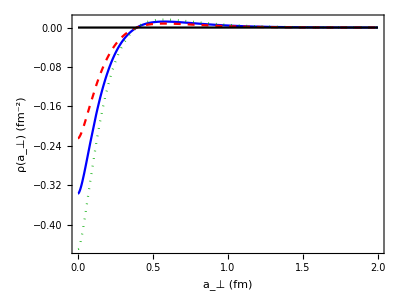

```mathematica
figrhoneutron=Plot[{1/0.197^2 rhoneutron[{a^2/0.197^2},{0.5482^2,0.531,1.5}],1/0.197^2 rhoneutron[{a^2/0.197^2},{0.5482^2,0.531,1.0}],1/0.197^2 rhoneutron[{a^2/0.197^2},{0.5482^2,0.531,2.0}],0},{a,0,2},PlotRange->{{0,2},Full},AspectRatio->0.75,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->{{Blue,Thickness[0.004]},{Red,Dashed,Thickness[0.004]},{Darker[Green],Dotted,Thickness[0.004]},{Black,Thickness[0.004]}},FrameTicksStyle->18,FrameLabel->{Style["a_⊥ (fm)",20,FontFamily->"Times"],Style["ρ(a_⊥) (fm^-2)",20,FontFamily->"Times"]}]
```

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/rhoneutron.pdf",figrhoneutron,"PDF"]
```

/Users/user/Liu/Repos/LFHQCD/evolution-more/notebook/rhoneutron.pdf

## Test